## FakeRegionPlot examples

### Setup

```mathematica
SetDirectory@NotebookDirectory[];
<<"FakeRegionPlot`"
```

A function for plotting regions:

```mathematica
ell[d_,h_]:=(x+d)^2+2(y+h)^2<2
ell[d_]:=ell[d,0]
```

## The problem

Mathematica's RegionPlot suffers a flaw when being exported to EPS: the transparency of its overlapping regions is broken because PostScript does not support transparent objects. Here's an example of what happens (with Mathematica output and EPS output, respectively):

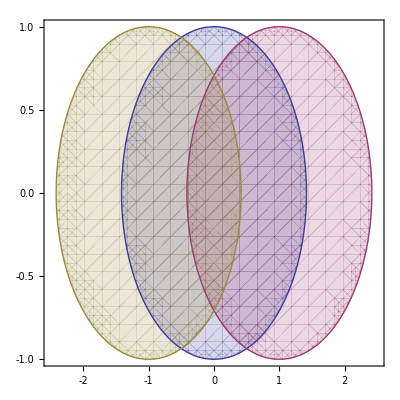
{-Graphics-,-Graphics-}

```mathematica
rr=RegionPlot[{ell[0],ell[-1],ell[1]},{x,-2.5,2.5},{y,-1,1}];
Export["regionplot.eps",rr];
ss=Show@Import["regionplot.eps"];
{rr,ss}
```

## The solution

Here's a hack to solve the problem. Rather than plotting the regions with transparent objects so their overlap is clearly visible, we plot every combination of region overlap separately, calculating the colour it should be as we go. The transparency calculation works okay, but could do with some improvement.

```mathematica
rr=FakeRegionPlot[{ell[0],ell[-1],ell[1]},{x,-2.5,2.5},{y,-1,1},PlotStyle->Lighter/@{Blue,Red,Green}];
Export["regionplot.eps",rr];
ss=Show@Import["regionplot.eps"];
{rr,ss}
```

{-Graphics-,-Graphics-}

## Examples

Defaults:

```mathematica
FakeRegionPlot[{ell[0],ell[-1],ell[1]},{x,-2.5,2.5},{y,-1,1}]
```

-Graphics-

More colourful, overriding the default boundary colours:

```mathematica
FakeRegionPlot[{ell[0],ell[-1],ell[1]},{x,-2.5,2.5},{y,-1,1},PlotStyle->{Blue,Red,Green},BoundaryStyle->Black]
```

-Graphics-

Customising the transparency:

```mathematica
FakeRegionPlot[{ell[0],ell[-1],ell[1],ell[0,1],ell[-1,1],ell[1,1]},{x,-2.5,2.5},{y,-1,1},
PlotStyle->{Blue,Blue,Blue,Red,Red,Red},BoundaryStyle->Black,Lighten->0.2]
```

-Graphics-